```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear :: wrsym will be suppressed during this calculation.

```mathematica
<<data`;
<<Matcher`;
<<classifier`;
```

```mathematica
(* so first, we just use the track of matrix, it is J1*)
```

```mathematica
BeginPackage["W`PCA`"];
J1::usage="J1";
mPCA::usage="";

Begin["`PP`"];
```

```mathematica
(* ss has dim of m*n*l, m classes and n samples each, each sample is l vector*)
J1[ss_]:=Module[
{Sw,Sb,m,mm},
mm=Map[Mean[#]&,ss];
Sw=Total[Map[Covariance[#]&,ss]];
If[Length[Sw]>0,Sw=Tr[Sw]];
m=Mean[Flatten[ss,1]];

If[Length[m]>0,
Sb=Total[Map[(#-m).(#-m)&,mm]],
Sb=Total[Map[(#-m)*(#-m)&,mm]]];
Sb/Sw];
(* outpou: Eigenvectors, Eigenvalues , pcs*)
mPCA[ss_]:=Module[
{lambda,ev,ppc,psc,tvp,stm},
(* this is how PCA works in math....*)
(*tvp, each row is a vector*)
{psc,tvp}=Chop[KarhunenLoeveDecomposition[ssᵀ,"Centered"->True]];
psc=pscᵀ;
(*Standardize[ss,Mean,1&].tvpᵀ==psc*)
lambda=Chop[Eigenvalues[Covariance[ss]]];
(* result is also raw-wised*)
{tvp,lambda,psc}
];
```

```mathematica
End[];
EndPackage[];
```

```mathematica
data=nxrData[-1];
Dimensions[data]
```

{50,2,6,46}

```mathematica
fft=Flatten[data,{{1,2},{3,4}}];
Dimensions[fft]
```

{100,276}

```mathematica
(* each row is a sample*)
(*sample=Transpose[fft];*)
sample=fft;
```

```mathematica
(*Needs["MultivariateStatistics`"];*)
```

```mathematica
Chop[sample]==sample
```

True

```mathematica
Chop[Mean[sample]];
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*Covariance[sample];
Dimensions[%]*)
```

```mathematica
(*od=Ordering[cv];
i=1;
While[Total[cv[[Ordering[cv,-i]]]]/Total[cv]<0.8,i++]
Total[cv[[Ordering[cv,-5]]]]/Total[cv]
*)
```

```mathematica
pc=PrincipalComponents [sample];
Dimensions[pc]
```

{100,276}

```mathematica
{tm,l,p}=mPCA[sample];
(*Chop[Table[Total[pc[[All,i]]],{i,Length[pc[[1]]]}]]*)
```

```mathematica
(* only 99 nonzero pcs*)
```

```mathematica
Length[Select[l,#≠0&]]
```

99

```mathematica
p[[;;,100;;102]]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
tpc=pc[[All,;;99]];
```

```mathematica
(*pps=tpc[[;;,;;3]];*)
```

```mathematica
(*ListPlot3D[pps]*)
```

```mathematica
(* pick only one factor*)
p1=tpc[[;;,1]];
sp1=Partition[p1,2];
Dimensions[%]
```

{50,2}

```mathematica
{ddiff,dsame}=eucDist[sp1];
{ns,nd}={Length[dsame],Length[ddiff]};
```

```mathematica
Min[dsame]
Max[dsame]
mdsame=Mean[dsame]
ddsame=StandardDeviation[dsame]

Min[ddiff]
Max[ddiff]
mddiff=Mean[ddiff]
dddiff=StandardDeviation[ddiff]
```

0.0530253

19.2825

2.31646

3.73844

0.000387055

72.4785

16.3364

13.3384

```mathematica
dx=0.4;
dds=BinCounts[dsame,{0,60,dx}]/ns;
ddd=BinCounts[ddiff,{0,60,dx}]/nd;

dist=Table[i*dx,{i,0,Length[ddd]-1}];
pdds=Transpose[{dist,dds}];
pddd=Transpose[{dist,ddd}];
```

```mathematica
pdata=sp1[[All,1]];
templ=sp1[[All,2]];
tg=ConstantArray[ConstantArray[0,Length[templ]],Length[pdata]];
For[i=1;k=1;n=1,i≤Length[pdata],i++,
For[m=1,m≤1,m++,
tg[[n,k]]=1;
n++;
];
k++;
];
```

```mathematica
EER[pdata,templ,tg,classifyDist1,{0,10,0.01}]
```

{3.29,{0.148163,0.14}}

```mathematica
pg=classifyDist1[pdata,templ,3.282];
VF[tg,pg]
```

{0.1484,0.148571,0.14}

```mathematica
mf[x_]:=VF[tg,classifyDist1[pdata,templ,x]][[1]];
```

```mathematica
mf[1.5]
```

0.074

```mathematica
(* as there are few samples in one class,it is hard to use error rate here*)
(*Minimize[{-mf[x],x>1&&x∈Reals},x]*)
```

{-0.02,{x→1.}}

```mathematica
(*feer[pdata_,templ_,tg_]:=Module[
{rr,de,tde=1,i,mr},
For[i=0,i<5,i=i+0.005,
rr=VF[tg,classifyDist1[pdata,templ,i]][[{2,3}]];
de=Abs[rr[[1]]-rr[[2]]];
If[de<=tde,tde=de;mr=rr,Break[]]];
{mr,tde}
];*)
```

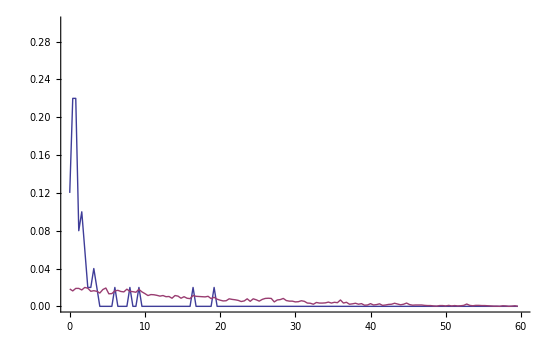

```mathematica
ListPlot[{pdds,pddd},Joined->True,PlotRange->{{0,60},{0,0.3}}]
```

```mathematica
(* use a few more factors*)
```

```mathematica
ps=tpc[[;;,1;;10]];
sps=Partition[ps,2];
Dimensions[%]
```

{50,2,10}

```mathematica
{ddiff,dsame}=eucDist[sps];
{ns,nd}={Length[dsame],Length[ddiff]};
```

```mathematica
dx=0.4;
dds=BinCounts[dsame,{0,60,dx}]/ns;
ddd=BinCounts[ddiff,{0,60,dx}]/nd;

dist=Table[i*dx,{i,0,Length[ddd]-1}];
pdds=Transpose[{dist,dds}];
pddd=Transpose[{dist,ddd}];
```

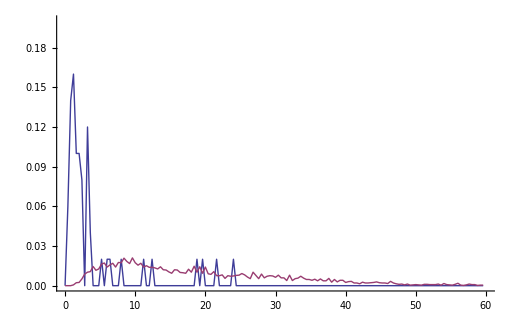

```mathematica
ListPlot[{pdds,pddd},Joined->True,PlotRange->{{0,60},{0,0.2}}]
```

```mathematica
pdata=sps[[All,1]];
templ=sps[[All,2]];
tg=ConstantArray[ConstantArray[0,Length[templ]],Length[pdata]];
For[i=1;k=1;n=1,i≤Length[pdata],i++,
For[m=1,m≤1,m++,
tg[[n,k]]=1;
n++;
];
k++;
];
```

```mathematica
pg=classifyDist1[pdata,templ,6.729];
```

```mathematica
VF[tg,pg]
```

{0.14,0.14,0.14}

```mathematica
(* relation of number of features and EER*)

geteer[s_,tg_,fc_]:=Module[
{pdata,templ},
pdata=s[[All,1]];
templ=s[[All,2]];

EER[pdata,templ,tg,fc,{0,10,0.005}]
];

tg=ConstantArray[ConstantArray[0,Length[templ]],Length[pdata]];
For[i=1;k=1;n=1,i≤Length[pdata],i++,
For[m=1,m≤1,m++,
tg[[n,k]]=1;
n++;
];
k++;
];
```

```mathematica
n=1;
ps=Partition[tpc[[;;,1;;n]],2];
Dimensions[ps]
```

{50,2,1}

```mathematica
(*e=Reap[For[i=1,i≤Length[tpc[[1]]],i++,
Sow[Mean[geteer[Partition[tpc[[;;,;;i]],2],tg,classifyDist1][[2]]]];
Print[i];]][[2,1]];*)
```

```mathematica
ee=Import["Cache_edat.mx"];
```

```mathematica
Dimensions[ee]
```

{99}

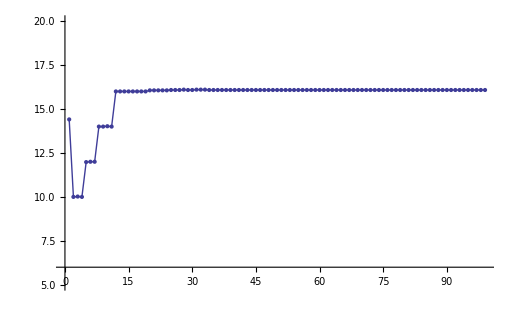

```mathematica
ListPlot[100*ee,Joined->True,PlotRange->{5,20},Mesh->Full]
```

```mathematica
(* select more effective pcs use MDA*)
```

```mathematica
spc=Partition[tpc,2];
Dimensions[%]
```

{50,2,99}

```mathematica
(*scatter matrix of all pcs*)
(*Sw=Tr[Total[Map[Covariance[#]&,spc]]];
Dimensions[%]
m=Mean[tpc];
mm=Map[Mean[#]&,spc];
Sb=Total[Map[(#-m).(#-m)&,mm]];
Dimensions[%]*)
```

{}

{}

```mathematica
(*spc2=Partition[tpc[[All,1]],2];
Dimensions[%]*)
```

{50,2}

```mathematica
(*Sw=Total[Map[Covariance[#]&,spc2]];

m=Mean[tpc[[All,1]]];
Flatten[spc2,1];
mm=Map[Mean[#]&,spc2];
Mean[mm];
Sb=Total[Map[(#-m)*(#-m)&,mm]];*)
```

```mathematica
(* this will not change even standardized PC*) 
sj1=Table[J1[Partition[tpc[[All,i]],2]],{i,Length[tpc[[1]]]}];
```

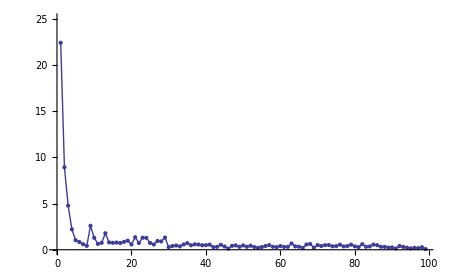

```mathematica
ListPlot[sj1,Joined->True,Mesh->Full,PlotRange->{0,25}]
```

```mathematica
(* features which have j1>1*)
ind=Reverse[Ordering[sj1]]
Length[ind]
```

{1,2,3,9,4,13,21,29,23,10,24,5,19,27,28,18,6,14,16,15,12,25,22,17,35,63,11,68,82,7,37,20,26,34,67,38,85,79,76,41,44,73,57,70,40,72,86,36,39,48,50,32,52,47,8,92,71,31,56,78,60,75,74,64,33,80,77,84,45,83,65,51,87,58,49,62,43,88,61,93,53,55,59,42,30,81,98,90,89,69,94,54,96,66,97,95,91,46,99}

99

```mathematica
stpc=tpc[[All,ind]];
```

```mathematica
J1[Partition[stpc,2]]
```

9.74995

```mathematica
(* what if pcs are ordered by MDA*)
```

```mathematica
(*t1=AbsoluteTime[];
e=Reap[For[i=1,i≤Length[stpc[[1]]],i++,
Sow[Mean[geteer[Partition[stpc[[;;,;;i]],2],tg,classifyDist1][[2]]]];
Print[i];]][[2,1]];
t2=AbsoluteTime[]-t1*)
```

```mathematica
e=Import["Cache_ePcamda.mx"];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

3337.296875

```mathematica
(*Export["Cache_ePcamda.mx",e];*)
```

```mathematica
(*The result seems much better*)
```

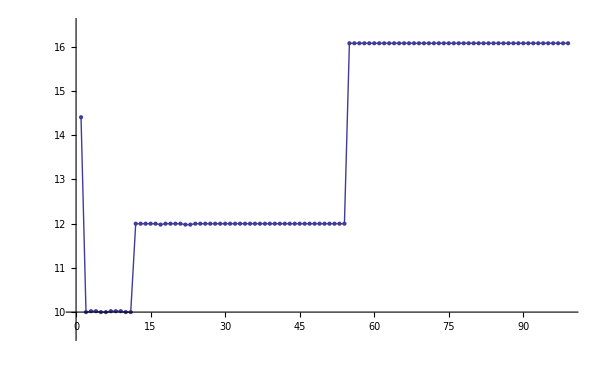

```mathematica
ListPlot[100*e,Joined->True,Mesh->Full,PlotRange->{9.5,16.5}]
e[[;;11]]
```

```mathematica
(*use 50 persons' one measure as a sample, how to compare same person's measure?*)
(* leave it to further research when there are enough data*)
```

```mathematica
fft1=Flatten[data[[All,1]],{{1},{2,3}}];
fft2=Flatten[data[[All,2]],{{1},{2,3}}];
Dimensions[fft1]
```

{50,276}

```mathematica
sample=fft1;
test=fft2;
```

```mathematica
pc1=PrincipalComponents [sample];
```

```mathematica
ssam=StdP[sample];
```

```mathematica
{tt,v,mpc1}=mPCA[sample];
Dimensions[%]
```

```mathematica
Dimensions[tt]
```

{276,276}

```mathematica
Chop[ssam.ttᵀ]==mpc1
```

True

```mathematica
Chop[mpc1-ssam.ttᵀ][[All,;;100]];
```

```mathematica
pmm=Mean[sample];

stest=Table[test[[i]]-pmm,{i,Length[test]}];
ptest=stest.ttᵀ;
```

```mathematica
indd={1,2,3,9,4,13,21,29,23,10,24};
```

```mathematica
ddiff=Reap[For[i=1,i<=Length[ptest]-1,i++,
For[j=i+1,j<=Length[ptest],j++,
Sow[EuclideanDistance[ptest[[i]],ptest[[j]]]];
]]
][[2,1]];
```

```mathematica
Min[ddiff]
```

1.52115

```mathematica
geteer[Partition[stpc11,2],tg,classifyDist1]
```

{5.355,{0.1,0.1}}